```mathematica
(*ML Data*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLF1MathematicaReads.xlsx"];
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

84

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

84

```mathematica
(*fitting to 90% of the data*)
n90=Floor[nΔYVec (0.9)]
```

75

```mathematica
(*Covariates*)


(*Yield Curve*)
X8Vec=Data[[1,All,3]];

(*Norfarm Jobs*)
X2Vec=Data[[1,All,4]];

(*Federal Funds*)
X3Vec=Data[[1,All,5]];

(*Mortgage Rate*)
X4Vec=Data[[1,All,6]];

(*Personal Consumption Expeditures*)
X5Vec=Data[[1,All,7]];

(*Industrial Production*)
X6Vec=Data[[1,All,8]];

(*Consumer Price Index*)
X7Vec=Data[[1,All,9]];

(*Crude Oil Prices*)
X8Vec=Data[[1,All,10]];

(*NASDAQ Composite Index*)
X9Vec=Data[[1,All,11]];
```

```mathematica
(*Plot Y - Observed data*)
```

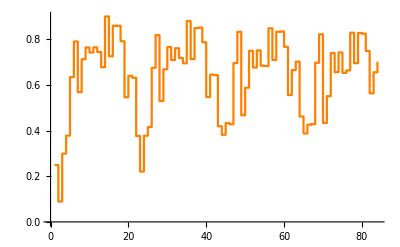

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Orange]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=2)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 YVec[[i-1]] +β8 X1[[i-1]]+β9 X2[[i-1]]+β10 X3[[i-1]]+β11 X4[[i-1]]  ))/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];
Dβ4=Simplify[D[LnL,β4]];


Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];
Dβ9=Simplify[D[LnL,β9]];
Dβ10=Simplify[D[LnL,β10]];
Dβ11=Simplify[D[LnL,β11]];


Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ7},{0==Dβ8},{0==Dβ9},{0==Dβ10},{0==Dβ11},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β7,0.1},{β8,0.1},{β9,0.1},{β10,0.1},{β11,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦2⟧ is longer than depth of object.

Part::partd: Part specification X2⟦2⟧ is longer than depth of object.

Part::partd: Part specification X3⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→-6.74696,β1→0.0983378,β2→0.00876501,β3→-0.020207,β4→0.0000302457,β7→-0.639257,β8→-0.0229107,β9→0.0114997,β10→-0.036012,β11→-0.0000755734,σ→6.40044×10^102}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 YVec[[i-1]] +β8 X1[[i-1]]+β9 X2[[i-1]]+β10 X3[[i-1]]+β11 X4[[i-1]];
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]]};
For[k=2,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

{0.,0.0482301,0.213711,0.061681,0.206029,0.154809,-0.243278,0.198285,-0.00168019,-0.0330991,-0.0195352,-0.0345172,-0.0452397,0.225623,-0.209192,0.111726,-0.0275062,-0.0649413,-0.19044,0.0337885,0.0280534,-0.254985,-0.0332295,0.129696,0.0116865,0.181963,0.128487,-0.261168,0.223015,0.0266407,-0.0341429,0.00142769,-0.0320358,-0.0283441,0.214584,-0.196477,0.119679,-0.0209121,-0.0597092,-0.187571,0.0328986,0.0245782,-0.262363,-0.0606377,0.0267257,-0.0238727,0.174244,0.115492,-0.270304,0.263006,0.0781464,-0.0237186,0.0226503,-0.0258258,-0.00678168,0.222391,-0.175989,0.122076,-0.010553,-0.0488737,-0.174777,0.0274243,0.0119907,-0.299974,-0.0878622,0.0230418,-0.0192697,0.173971,0.114524,-0.263277,0.284398,0.101908,-0.0175456,0.0355295,-0.0202837,0.0134509,0.234589,-0.163617,0.130918,-0.00704762,-0.0426573,-0.163125,0.0227546,0.0181273}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.249077,0.297307,0.511018,0.572699,0.778728,0.933537,0.690259,0.888544,0.886864,0.853765,0.834229,0.799712,0.754472,0.980096,0.770904,0.882629,0.855123,0.790182,0.599742,0.633531,0.661584,0.4066,0.37337,0.503066,0.514753,0.696716,0.825203,0.564035,0.78705,0.813691,0.779548,0.780976,0.74894,0.720596,0.93518,0.738703,0.858382,0.837469,0.77776,0.590189,0.623088,0.647666,0.385303,0.324665,0.351391,0.327519,0.501762,0.617254,0.34695,0.609956,0.688102,0.664383,0.687034,0.661208,0.654426,0.876817,0.700828,0.822904,0.812351,0.763477,0.5887,0.616125,0.628115,0.328141,0.240279,0.263321,0.244051,0.418022,0.532546,0.269269,0.553667,0.655576,0.63803,0.673559,0.653276,0.666727,0.901315,0.737698,0.868616,0.861568,0.818911,0.655786,0.67854,0.696668}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.249077},{2,0.297307},{3,0.511018},{4,0.572699},{5,0.778728},{6,0.933537},{7,0.690259},{8,0.888544},{9,0.886864},{10,0.853765},{11,0.834229},{12,0.799712},{13,0.754472},{14,0.980096},{15,0.770904},{16,0.882629},{17,0.855123},{18,0.790182},{19,0.599742},{20,0.633531},{21,0.661584},{22,0.4066},{23,0.37337},{24,0.503066},{25,0.514753},{26,0.696716},{27,0.825203},{28,0.564035},{29,0.78705},{30,0.813691},{31,0.779548},{32,0.780976},{33,0.74894},{34,0.720596},{35,0.93518},{36,0.738703},{37,0.858382},{38,0.837469},{39,0.77776},{40,0.590189},{41,0.623088},{42,0.647666},{43,0.385303},{44,0.324665},{45,0.351391},{46,0.327519},{47,0.501762},{48,0.617254},{49,0.34695},{50,0.609956},{51,0.688102},{52,0.664383},{53,0.687034},{54,0.661208},{55,0.654426},{56,0.876817},{57,0.700828},{58,0.822904},{59,0.812351},{60,0.763477},{61,0.5887},{62,0.616125},{63,0.628115},{64,0.328141},{65,0.240279},{66,0.263321},{67,0.244051},{68,0.418022},{69,0.532546},{70,0.269269},{71,0.553667},{72,0.655576},{73,0.63803},{74,0.673559},{75,0.653276},{76,0.666727},{77,0.901315},{78,0.737698},{79,0.868616},{80,0.861568},{81,0.818911},{82,0.655786},{83,0.67854},{84,0.696668}}

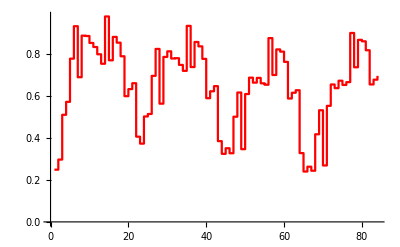

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->0, Joined->True,PlotStyle->Red,PlotRange->All]
```

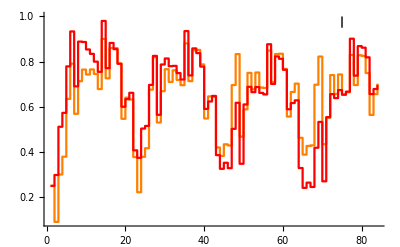

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)

A=Show[{YObserved,YPredictedPlotInt},Graphics[{Black, Line[{{n90,0.95},{n90,1}}]}],PlotRange->All]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.812665

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0238647

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

0.00238647

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->6
```

0.523478